```mathematica
(*H1x*)
SetDirectory["/Users/aditya/Downloads/vortex"]
m = 0.50; 
lam = 1;(* next nearest neighbour hopping (diagonal)*)
t[0][0] = 3/2*m;
t[-1][0] = -m;
t[0][-1] = -m;
t[1][0] = -m;
t[0][1] = -m;
t[-1][-1] = m/4;
t[1][-1] = m/4;
t[-1][1] = m/4;
t[1][1] = m/4;
(*SOC spinorbit*)
l[-1][0] = lam(1-I);
l[0][-1] = lam(1-I);
l[1][0] = lam(1-I);
l[0][1] = lam(1-I);
Nx = 20;
Ny = 20;
i = 0;

For[ix = 1, ix <= Nx, ix++,
 For[iy = 1, iy <= Ny, iy++, i++;
  xpos[i] = ix;
  ypos[i] = iy;]]
NN = i;

Vimp = 0;
empty= SparseArray[{x_, y_} -> 0, {NN, NN}];
(*Hopping Matrix*)
tijmn = Table[
   If[NumericQ[t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)]], t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)],
    If[NumericQ[t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])]], t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])],
     If[NumericQ[t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)]], t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)],
      If[NumericQ[t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)]], t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)],
       If[NumericQ[t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])]], t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])],
        If[NumericQ[t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)]], t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)],
         If[NumericQ[t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)]], t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)],
          If[NumericQ[t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])]], t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])],
           If[NumericQ[t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]], t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]]]]]]]]]],
   {i, 1, NN}, {j, 1, NN}];
For[i = 1, i <= NN, i++,
  For[j = 1, j <= NN, j++,
   tij[i][j] = tijmn[[j, i]]
   ]];
Clear[tijmn]
H1= SparseArray[{x_, y_} /; NumericQ[tij[x][y]] -> tij[x][y], {NN, NN}];
tijmn = Table[
   If[NumericQ[l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)]], l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)],
    If[NumericQ[l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])]], l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])],
     If[NumericQ[l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)]], l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)],
      If[NumericQ[l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)]], l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)],
       If[NumericQ[l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])]], l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])],
        If[NumericQ[l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)]], l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)],
         If[NumericQ[l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)]], l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)],
          If[NumericQ[l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])]], l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])],
           If[NumericQ[l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]], l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]]]]]]]]]],
   {i, 1, NN}, {j, 1, NN}];
For[i = 1, i <= NN, i++,
  For[j = 1, j <= NN, j++,
   tij[i][j] = tijmn[[j, i]]
   ]];
Clear[tijmn]
soc= SparseArray[{x_, y_} /; NumericQ[tij[x][y]] -> tij[x][y], {NN, NN}];
Clear[mu]
Chempot1[mu_]:= SparseArray[{x_, x_} ->  -mu, {NN, NN}];
(*Chempot2[mu_]:= SparseArray[{y_, y_} ->  -mu, {NN, NN}];*)
(*Chempot[mu]=ArrayFlatten[{{Chempot1[mu], empty}, {empty,Chempot1[mu]}}];*)
Hop1x[mu_]:= ArrayFlatten[{{H1-Chempot1[mu],soc}, {ConjugateTranspose[soc], -H1-Chempot1[mu]}}];(*adding pauli matrix σx*)
(*HermitianMatrixQ[Hop1x[0]];
MatrixForm[Hop1x[]];*)
```

/Users/aditya/Downloads/vortex

```mathematica
(*------onsite------*)
Clear[s,st,stab,sij,SCs,dmn,dmm]

js={};
For[i=1,i<=NN,i++,jisel={};
For[j=1,j<=NN,j++,
If[xpos[i]==xpos[j],
If[ypos[i]==ypos[j],AppendTo[jisel,j]]]];AppendTo[js,jisel]]



SCs1=SparseArray[{x_,y_}/;Not[TrueQ[sij[x][y]==Null]]->0,{NN,NN}];
SCs2[st_]:= SparseArray[{Band[{1,1}]-> Flatten[st]}, {NN, NN}];
SCs3=SparseArray[{x_,y_}/;Not[TrueQ[sij[x][y]==Null]]->0,{NN,NN}];
SCs[st_]:= ArrayFlatten[{{SCs1, SCs2[st]}, {SCs2[st], SCs1}}];
Clear[sij]
s[i_,j_]:=Take[st[[i,j]]];
```

```mathematica
f[x_]:=1./(Exp[x/kT]+1.);
kT = 0.001 (*eV*);
f[x_] :=(*UnitStep[x]*)(*1./(Exp[x/kT]+1.);*)If[Re[x] > 0.02, 0.0,
   If[Re[x] < -0.02, 1.0,
    1./(Exp[Re[x]/kT] + 1.)]];

(*mtuss={};*)
(*For[k=0,k≤0.2,k=k+0.1,
Print[StringJoin["calculte..",ToString[k]]];*)
(*flag1 = 1;*)
(*m = 0.5*0;*)
(*Us = 0.0;*)
vs = -1.45;(*s-wave pairing interaction*)
(*vd = -0.2*0; d-wave pairing interaction*)
mu = 0;

nexp = 1.2; (*expected electro density in your system*)
(*ntot = 1;
nut=Table[(ntot/2.)+((m*(-1)^(xpos[i]+ypos[i]))/2),{i,1,NN}];
ndt=Table[(ntot/2.)-((m*(-1)^(xpos[i]+ypos[i]))/2),{i,1,NN}];*)

Clear[v,as,b,bm];

(*dsignn={}; (*initialisation of d-wave sign*)
For[i=1,i<=NN,i++,jisel={};
For[j=1,j<=NN,j++,
If[xpos[i]==xpos[j],
If[ypos[i]==ypos[j]+1,AppendTo[jisel,-1],
If[ypos[i]==ypos[j]-1,AppendTo[jisel,-1],
If[ypos[i]==ypos[j]+(Ny-1),AppendTo[jisel,-1],
If[ypos[i]==ypos[j]-(Ny-1),AppendTo[jisel,-1]]]]],
If[ypos[i]==ypos[j],
If[xpos[i]==xpos[j]+1,AppendTo[jisel,1],
If[xpos[i]==xpos[j]-1,AppendTo[jisel,1],
If[xpos[i]==xpos[j]+(Nx-1),AppendTo[jisel,1],
If[xpos[i]==xpos[j]-(Nx-1),AppendTo[jisel,1]]]]]]]];
AppendTo[dsignn,jisel]];
spmtnn=Table[dsignn[[i,j]]*dijnn,{i,1,NN},{j,1,4}];
dijnn=0.3;*)

st=Table[ds,{i,1,NN},{j,1}]; (*initialisation of s-wave*)
ds=-0.01; (*Gap size*)
(*AbsoluteTiming[*)
(*MatrixForm[SCs[st]]*)
```

```mathematica
(*
 Huu = Ho (*+imp*)(**+Hartree*);
  Hvv = -ConjugateTranspose[Ho (*-imp*)(*+Hartree2*)];
  Huv= SCs[st]; (*Superconducting part Δ*)
  Hvu=ConjugateTranspose[Huv];
  H = ArrayFlatten[{{Huu, Huv}, {Hvu, Hvv}}]; 
MatrixForm[H];*)
```

```mathematica
(*calculation mean fields via iteration*)(*Main Hamiltonian BDG*)
iter = 100;
  (*em =  SparseArray[{x_, x_} -> 0, {NN, NN}];*)
For[a = 1, a <= iter, a++,
  (*mtus={};*)
  Huu = H1-Chempot1[mu] (*+imp*)(**+Hartree*);
  Hdd = H1-Chempot1[mu];
Hud = soc;
Hdu = Conjugate[soc];
hh1 = ArrayFlatten[{{Huu,Hud}, {Hdu, Hdd}}];
hh2 = ArrayFlatten[{{-Conjugate[Huu],Conjugate[Hud]}, {Conjugate[Hdu], -Conjugate[Hdd]}}];
    Huv= SCs[st]; (*Superconducting part Δ*)
  Hvu=Conjugate[Huv];
  H = ArrayFlatten[{{hh1, Huv}, {Hvu, hh2}}]; (*Joins all the matrices*)
 (* Print[HermitianMatrixQ[H]];*)
  (*Print[MatrixForm[H]];*)
  
  ES = Eigensystem[H];
 
  fermi = Map[f, ES[[1]]];
  (*tab = Table[1,{i,Length[fermi]}];*)
  nutcalc = Table[((Abs[ES[[2]][[;; , i]]])^2.) . fermi, {i, 1, NN}];
  
  
  ndtcalc = Table[((Abs[ES[[2]][[;; , i + 3NN]]])^2.) . (1. - fermi), {i, 1, NN}];
  
  
  ni = nutcalc + ndtcalc;
  mi = nutcalc - ndtcalc;
  nt = Total[ni]/NN;
  mt = Total[Abs[mi]]/NN;
  
  
  
  (*Print["till here"];*)
  stcalc=Table[vs*((Inner[Times,ES[[2]][[;;,i]],Conjugate[ES[[2]][[;;,j+
  3NN]]],List])+(Inner[Times,ES[[2]][[;;,i+NN]],Conjugate[ES[[2]][[;;,i+
  2NN]]],List])).fermi,{i,1,NN},{j,js[[i]]}];
  (*
vsite = 378;
  l=0.3;(*penetration depth*)
  zetanot=l/Pi;(*coherence length*)
    stcalc=Table[
  If[xpos[i]==xpos[vsite],
  phi=Pi/2,
  phi=ArcTan[(Abs[ypos[i]-ypos[vsite]])/(Abs[xpos[i]-xpos[vsite]])];
  ];
  vs*((Inner[Times,ES[[2]][[;;,i]],Conjugate[ES[[2]][[;;,j+
  3NN]]],List])+(Inner[Times,ES[[2]][[;;,i+NN]],Conjugate[ES[[2]][[;;,i+
  2NN]]],List])).fermi*
  Tanh[Sqrt[(xpos[i]-xpos[vsite])^2+(ypos[i]-ypos[vsite])^2]/zetanot]*
  Exp[I*phi]
,{i,1,NN},{j,js[[i]]}];
*)

  (*spmtcalcnn=Table[vd*((Inner[Times,ES[[2]][[;;,i]],ES[[2]][[;;,j+
  NN]],List])+(Inner[Times,ES[[2]][[;;,j]],ES[[2]][[;;,i+
  NN]],List])).fermi,{i,1,NN},{j,jspmnn[[i]]}];*)
  
  
  sta=Total[Flatten[stcalc]]/NN;(*
  stann=Total[Total[Abs[spmtcalcnn]]]/NN*0.25;*)
  
  
  
  Print[a , " mu=", mu, "  mt=", mt,(*" Us=", Us,*)"  n=", nt ,"  sup=", Abs[ sta(*"  supnn=",  stann*)]];
  mu = mu - 0.1*(nexp - nt);
  (*nut=0.5*nutcalc+0.5*nut;
  ndt=0.5*ndtcalc+0.5*ndt;*)
  st=0.5*stcalc+0.5*st;
  (*spmtnn=0.5*spmtcalcnn+0.5*spmtnn;*)
  ];
(*AppendTo[mtuss,{vd,stann}];
];*)


Export["Huu.wdx",Huu];
Export["Hud.wdx",Hud];
Export["Hdu.wdx",Hdu];
Export["Hdd.wdx",Hdd];
Export["SCs.wdx",SCs[st]];
```

1 mu=0  mt=4.61436×10^-16  n=0.804787  sup=0.00570491

2 mu=-0.0395213  mt=3.64708×10^-16  n=0.805039  sup=0.00497729

3 mu=-0.0790174  mt=3.99542×10^-16  n=0.805039  sup=0.00461301

4 mu=-0.118514  mt=4.74482×10^-16  n=0.855024  sup=0.0032253

5 mu=-0.153011  mt=4.93078×10^-16  n=0.87445  sup=0.00282286

6 mu=-0.185566  mt=1.24831×10^-15  n=0.894128  sup=0.00251586

7 mu=-0.216153  mt=4.67404×10^-16  n=0.905038  sup=0.00267708

8 mu=-0.24565  mt=4.44783×10^-16  n=0.905904  sup=0.00652354

9 mu=-0.275059  mt=4.73649×10^-16  n=0.915344  sup=0.00904623

10 mu=-0.303525  mt=4.53249×10^-16  n=0.947874  sup=0.0262295

11 mu=-0.328737  mt=4.87388×10^-16  n=0.95291  sup=0.02396

12 mu=-0.353447  mt=4.83502×10^-16  n=0.954635  sup=0.0244746

13 mu=-0.377983  mt=4.58245×10^-16  n=0.966384  sup=0.0302005

14 mu=-0.401345  mt=4.79894×10^-16  n=0.971898  sup=0.040902

15 mu=-0.424155  mt=4.87249×10^-16  n=0.985599  sup=0.0513935

16 mu=-0.445595  mt=4.6782×10^-16  n=0.994731  sup=0.0534896

17 mu=-0.466122  mt=4.70457×10^-16  n=1.00899  sup=0.0581835

18 mu=-0.485223  mt=4.5991×10^-16  n=1.0121  sup=0.059931

19 mu=-0.504012  mt=4.95992×10^-16  n=1.01512  sup=0.0619178

20 mu=-0.5225  mt=5.09315×10^-16  n=1.01856  sup=0.0647174

21 mu=-0.540644  mt=4.78784×10^-16  n=1.02297  sup=0.068413

22 mu=-0.558348  mt=4.89331×10^-16  n=1.02851  sup=0.0722541

23 mu=-0.575496  mt=4.724×10^-16  n=1.03461  sup=0.0750942

24 mu=-0.592035  mt=4.91551×10^-16  n=1.04038  sup=0.0765133

25 mu=-0.607998  mt=5.15699×10^-16  n=1.04549  sup=0.0768704

26 mu=-0.623449  mt=5.31797×10^-16  n=1.06961  sup=0.0820474

27 mu=-0.636488  mt=5.17641×10^-16  n=1.0733  sup=0.0834629

28 mu=-0.649159  mt=4.97102×10^-16  n=1.07691  sup=0.0844649

29 mu=-0.661468  mt=4.9627×10^-16  n=1.08061  sup=0.0851593

30 mu=-0.673407  mt=4.91829×10^-16  n=1.08443  sup=0.0855401

31 mu=-0.684964  mt=5.10147×10^-16  n=1.08882  sup=0.0856448

32 mu=-0.696082  mt=5.49283×10^-16  n=1.10217  sup=0.0873421

33 mu=-0.705865  mt=4.70179×10^-16  n=1.10567  sup=0.0869363

34 mu=-0.715298  mt=4.77951×10^-16  n=1.10907  sup=0.0858896

35 mu=-0.724392  mt=4.81004×10^-16  n=1.11236  sup=0.0842777

36 mu=-0.733156  mt=5.2458×10^-16  n=1.11553  sup=0.082171

37 mu=-0.741602  mt=5.31797×10^-16  n=1.11858  sup=0.0796312

38 mu=-0.749745  mt=5.05984×10^-16  n=1.12149  sup=0.0767109

39 mu=-0.757595  mt=4.88776×10^-16  n=1.12426  sup=0.0734542

40 mu=-0.765169  mt=5.2458×10^-16  n=1.12689  sup=0.0698988

41 mu=-0.77248  mt=4.98768×10^-16  n=1.12936  sup=0.066079

42 mu=-0.779545  mt=5.06262×10^-16  n=1.13166  sup=0.0620281

43 mu=-0.786379  mt=5.02931×10^-16  n=1.13378  sup=0.0577817

44 mu=-0.793001  mt=4.8711×10^-16  n=1.1357  sup=0.0533805

45 mu=-0.799431  mt=4.46865×10^-16  n=1.13743  sup=0.0488725

46 mu=-0.805688  mt=5.61495×10^-16  n=1.13895  sup=0.0443137

47 mu=-0.811793  mt=5.08482×10^-16  n=1.14026  sup=0.039768

48 mu=-0.817767  mt=5.02653×10^-16  n=1.14136  sup=0.0353047

49 mu=-0.823631  mt=5.30687×10^-16  n=1.14227  sup=0.0309939

50 mu=-0.829405  mt=4.90996×10^-16  n=1.14299  sup=0.026902

51 mu=-0.835106  mt=5.69267×10^-16  n=1.14355  sup=0.0230862

52 mu=-0.84075  mt=5.01821×10^-16  n=1.14398  sup=0.0195904

53 mu=-0.846352  mt=5.20972×10^-16  n=1.1443  sup=0.0164429

54 mu=-0.851923  mt=4.77673×10^-16  n=1.14452  sup=0.0136557

55 mu=-0.85747  mt=4.99323×10^-16  n=1.14468  sup=0.0112263

56 mu=-0.863002  mt=5.24303×10^-16  n=1.14479  sup=0.00913983

57 mu=-0.868522  mt=5.05151×10^-16  n=1.14487  sup=0.00737257

58 mu=-0.874035  mt=4.82947×10^-16  n=1.14492  sup=0.0058948

59 mu=-0.879544  mt=4.78784×10^-16  n=1.14495  sup=0.00467382

60 mu=-0.885049  mt=5.15976×10^-16  n=1.14497  sup=0.00367619

61 mu=-0.890552  mt=5.00433×10^-16  n=1.14498  sup=0.00286951

62 mu=-0.896054  mt=4.93494×10^-16  n=1.14499  sup=0.00222356

63 mu=-0.901555  mt=4.9627×10^-16  n=1.145  sup=0.00171115

64 mu=-0.907054  mt=6.30884×10^-16  n=1.14735  sup=0.00132825

65 mu=-0.91232  mt=7.8576×10^-16  n=1.16449  sup=0.00112864

66 mu=-0.915871  mt=9.91984×10^-16  n=1.17088  sup=0.000920267

67 mu=-0.918783  mt=5.68712×10^-16  n=1.1827  sup=0.000769861

68 mu=-0.920513  mt=4.87943×10^-16  n=1.18455  sup=0.000631388

69 mu=-0.922058  mt=5.21527×10^-16  n=1.1849  sup=0.000515617

70 mu=-0.923567  mt=5.3485×10^-16  n=1.18498  sup=0.00042015

71 mu=-0.92507  mt=4.724×10^-16  n=1.18499  sup=0.000341733

72 mu=-0.92657  mt=5.76483×10^-16  n=1.185  sup=0.000277468

73 mu=-0.92807  mt=5.28744×10^-16  n=1.185  sup=0.000224905

74 mu=-0.92957  mt=4.94882×10^-16  n=1.185  sup=0.000181991

75 mu=-0.93107  mt=5.10147×10^-16  n=1.185  sup=0.00014702

76 mu=-0.93257  mt=5.29299×10^-16  n=1.185  sup=0.000118573

77 mu=-0.93407  mt=5.14311×10^-16  n=1.185  sup=0.0000954731

78 mu=-0.93557  mt=5.15143×10^-16  n=1.185  sup=0.0000767485

79 mu=-0.93707  mt=4.80727×10^-16  n=1.185  sup=0.000061597

80 mu=-0.93857  mt=4.82947×10^-16  n=1.185  sup=0.0000493578

81 mu=-0.94007  mt=4.92106×10^-16  n=1.185  sup=0.0000394879

82 mu=-0.94157  mt=5.35127×10^-16  n=1.185  sup=0.0000315422

83 mu=-0.94307  mt=4.88221×10^-16  n=1.185  sup=0.0000251561

84 mu=-0.94457  mt=5.4845×10^-16  n=1.185  sup=0.000020032

85 mu=-0.94607  mt=5.44564×10^-16  n=1.185  sup=0.0000159273

86 mu=-0.94757  mt=5.17086×10^-16  n=1.185  sup=0.0000126445

87 mu=-0.94907  mt=4.82114×10^-16  n=1.185  sup=0.0000100233

88 mu=-0.95057  mt=5.31797×10^-16  n=1.185  sup=7.93358×10^-6

89 mu=-0.95207  mt=5.45952×10^-16  n=1.185  sup=6.27028×10^-6

90 mu=-0.95357  mt=5.20972×10^-16  n=1.185  sup=4.94843×10^-6

91 mu=-0.95507  mt=5.22082×10^-16  n=1.185  sup=3.89958×10^-6

92 mu=-0.95657  mt=5.30131×10^-16  n=1.185  sup=3.0686×10^-6

93 mu=-0.95807  mt=5.16809×10^-16  n=1.185  sup=2.41125×10^-6

94 mu=-0.95957  mt=5.52336×10^-16  n=1.185  sup=1.89203×10^-6

95 mu=-0.96107  mt=5.84532×10^-16  n=1.185  sup=1.48253×10^-6

96 mu=-0.96257  mt=5.74818×10^-16  n=1.185  sup=1.16004×10^-6

97 mu=-0.96407  mt=6.03684×10^-16  n=1.185  sup=9.06438×10^-7

98 mu=-0.96557  mt=5.90084×10^-16  n=1.185  sup=7.07306×10^-7

99 mu=-0.96707  mt=6.11178×10^-16  n=1.185  sup=5.51169×10^-7

100 mu=-0.96857  mt=5.54279×10^-16  n=1.185  sup=4.28918×10^-7

```mathematica
SortBy[ES[[1]]];
```

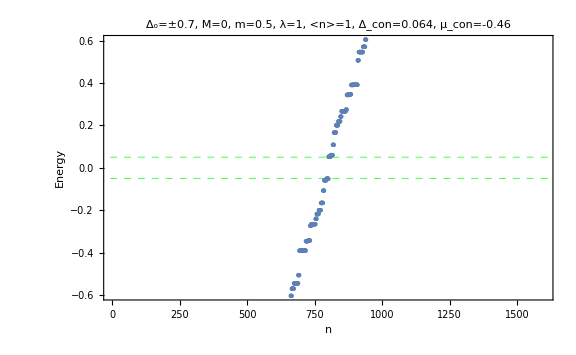

-Graphics-

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{-8.48098, -8.26976, -8.26976, -8.26976, -8.26976, -8.05976, -8.05976, -8.05976, «36», -6.50243, -6.50243, -6.25673, -6.25673, -6.25673, -6.25673, «1550»}, «9»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{-8.48098,-8.26976,-8.26976,-8.26976,-8.26976,-8.05976,-8.05976,-8.05976,«36»,-6.50243,-6.50243,-6.25673,-6.25673,-6.25673,-6.25673,«1550»},«9»]. An option must be a rule or a list of rules.

General::stop: Further output of ListPlot::nonopt will be suppressed during this calculation.

```mathematica
ListPlot[Sort[ES[[1]]],PlotRange->{-0.6,0.6} ,Frame->True,PlotLabel->"Δ_o=±0.7, M=0, m=0.5, λ=1, <n>=1, Δ_con=0.064, μ_con=-0.46 ",FrameLabel->{n,Energy},LabelStyle->"DisplayFormula",GridLines->{None,{-0.05,0.05}},GridLinesStyle->Directive[Green, Dashed], Frame->True, FrameStyle->Gray,ImageSize->Large]
```